```mathematica
equipotential[n_]:=DensityPlot[(Norm[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}]])^-1,{x,-7/6,7/6},{y,-7/6,7/6},MeshFunctions->{#3&,#3&},Mesh->{Range[0,0.1,0.01]~Join~Range[0.1,2,0.1]},MeshStyle->{{Yellow,Dashed}},PlotRange->{0,20},ColorFunction->"GrayTones",PlotPoints->{200,200},ImageSize->1000]
```

```mathematica
equipotential[6]
```

-Graphics-

```mathematica
Norm[Block[{n=3},Sum[{(x-Cos[2π i/n])/((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2),(y-Sin[2π i/n])/((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)},{i,1,n}]]]
```

√(Abs[(-1+x)/((-1+x)^2+y^2)+(1/2+x)/((1/2+x)^2+(-(√3)/2+y)^2)+(1/2+x)/((1/2+x)^2+((√3)/2+y)^2)]^2+Abs[y/((-1+x)^2+y^2)+(-(√3)/2+y)/((1/2+x)^2+(-(√3)/2+y)^2)+((√3)/2+y)/((1/2+x)^2+((√3)/2+y)^2)]^2)

```mathematica
equi[n_]:=DensityPlot[(Norm[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}]]),{x,-7/6,7/6},{y,-7/6,7/6},MeshFunctions->{#3&,#3&},Mesh->{Range[0,2,0.1]},MeshStyle->{{Yellow,Dashed}},PlotRange->{0,20},ColorFunction->"GrayTones",PlotPoints->{200,200},ImageSize->1000]
```

```mathematica
equi[5]
```

-Graphics-

```mathematica
VectorPlot
```

```mathematica
Block[{n=6},Show[DensityPlot[(Norm[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}]])^-1,{x,-7/6,7/6},{y,-7/6,7/6},MeshFunctions->{#3&,#3&},Mesh->{Range[0,0.1,0.01]~Join~Range[0.1,2,0.1]},MeshStyle->{{Yellow,Dashed}},PlotRange->{0,20},ColorFunction->"GrayTones",PlotPoints->{200,200},ImageSize->1000],StreamPlot[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}],{x,-7/6,7/6},{y,-7/6,7/6},StreamStyle->{Lighter[Purple],Arrowheads[0.01]},StreamPoints->1000,StreamScale->Tiny]]]
```

-Graphics-

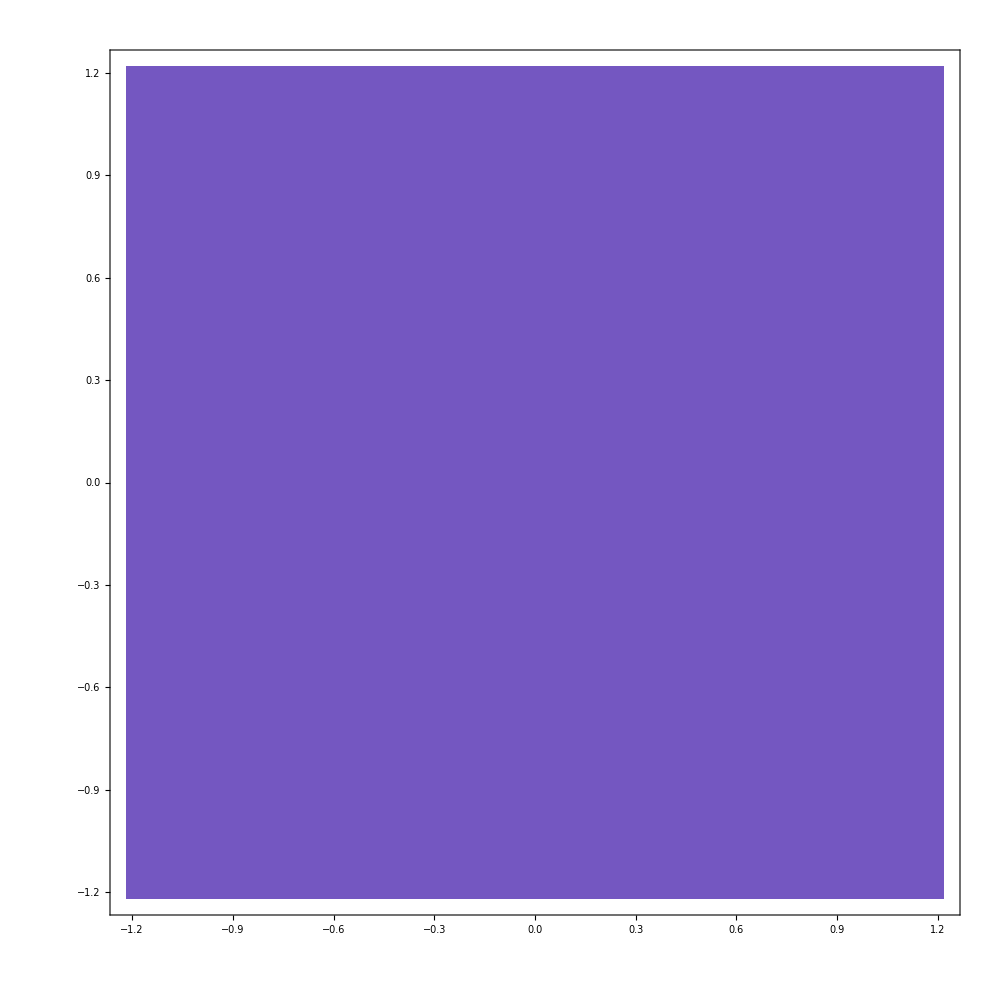

```mathematica
Block[{n=5},StreamDensityPlot[Sum[{{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},(Norm[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}]])^-1},{i,1,n}],{x,-7/6,7/6},{y,-7/6,7/6}(*,VectorPoints->30,StreamStyle->Darker[Red],VectorStyle->{Arrowheads[0.003],Darker[Red]},MeshFunctions->{#3&,#3&},Mesh->{Range[0,0.1,0.01]~Join~Range[0.1,2,0.1]},MeshStyle->{{Yellow,Dashed}},PlotRange->{0,20},ColorFunction->"GrayTones",ImageSize->1000*)]]
```

```mathematica
fieldandpotential[n_]:=Show[DensityPlot[(Norm[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}]])^-1,{x,-7/6,7/6},{y,-7/6,7/6},MeshFunctions->{#3&,#3&},Mesh->{Range[0,0.1,0.01]~Join~Range[0.1,2,0.1]},MeshStyle->{{Yellow,Dashed}},PlotRange->{0,20},ColorFunction->"GrayTones",PlotPoints->{200,200},ImageSize->1000],StreamPlot[Sum[{(x-Cos[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2)),(y-Sin[2π i/n])/(((x-Cos[2π i/n])^2+(y-Sin[2π i/n])^2)^(3/2))},{i,1,n}],{x,-7/6,7/6},{y,-7/6,7/6},StreamStyle->{Lighter[Purple],Arrowheads[0.01]},StreamPoints->1000,StreamScale->Tiny]]
```

```mathematica
fieldandpotential[6]
```

-Graphics-